```mathematica
(*Finite Element Method*)
```

```mathematica
(*Parameter initialization*)
SetDirectory[NotebookDirectory[]];

elemFilename="chnlelems.dat";
nodeFilename="chnlnodes.dat";
height=9;(*The number of elements on the left and right edge of the flow*)
origin = 61;(*Node ID of the location of the Dirichlet boundary singularity*)
inflow=1;(*Flow in and out of the left/right edges*)
scale=.5;(*Flow field arrow display scale*)
Δx=.01;(*Streamline resolution*)
Δy=.01;(*Streamline resolution*)
```

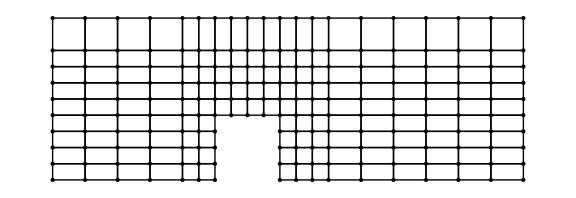

```mathematica
(*Geometry initialization*)

(*elementRecord[[i]] = The node element array for the ith element*)
(*elementRecord[[i]][[j - 1]] = The jth node of element i, counting from bottom left going counterclockwise*)(*Structure: The elements should be in a grid with the first column where the flow enters and the last column where the flow leaves.*)
elementRecord =Import[elemFilename];

(*nodeRecord[[i]] = The coordinates array for the ith node*)
(*nodeRecord[[i]][[j]] = The x or y coordinate of the node; x is j = 2, y is j = 3*)
nodeRecord=Import[nodeFilename];

(*Preliminary node layout*)
getNodes[i_]:=Delete[elementRecord[[i]],1];
getNodes::usage="Returns the nodes {N1, N2, N3, N4} of element i in counterclockwise order from the bottom left.";
getLocation[i_]:=Delete[nodeRecord[[i]],1];
getLocation::usage="Returns the coordinates {x, y} of node i.";

lineArray=ConstantArray[0,{Length[elementRecord]}];
pointArray=ConstantArray[0,{Length[nodeRecord]}];

(*For every element, draw the edges that make up the element*)
For[elt=1,elt≤Length[elementRecord],elt++,
α=getLocation[getNodes[elt][[1]]][[1]];
β=getLocation[getNodes[elt][[1]]][[2]];
γ=getLocation[getNodes[elt][[3]]][[1]];
δ=getLocation[getNodes[elt][[3]]][[2]];
(*Draw the rectangle from (α,β) to (γ,δ)*)
lineArray[[elt]]=Line[{{α,β},{γ,β},{γ,δ},{α,δ},{α,β}}];
]
(*For every node, add its coordinates to be drawn*)
For[node=1,node≤Length[nodeRecord],node++,
pointArray[[node]]=Point[{getLocation[node][[1]],getLocation[node][[2]]}];
]
(*Display the mesh*)
Show[Graphics[lineArray],Graphics[{PointSize[Large],pointArray}],ImageSize-> Large]
```

```mathematica
(*Basis polynomials*)
Ne[i_,α_,β_,γ_,δ_,x_,y_]:=Boole[i==1]*((γ-x)/(γ-α))*((δ-y)/(δ-β))+Boole[i==2]*((x-α)/(γ-α))*((δ-y)/(δ-β))+Boole[i==3]*((x-α)/(γ-α))*((y-β)/(δ-β))+Boole[i==4]*((γ-x)/(γ-α))*((y-β)/(δ-β))
Ne::usage="Basis polynomial. i is the corner index, starting at the bottom left and proceeding counterclockwise. (α,β) is the coordinate of the lower-left point, (γ,δ) is the upper-right point";
```

```mathematica
(*Matrix initialization*)
Kij =ConstantArray[0, {Length[nodeRecord],Length[nodeRecord]}];

(*Element loop: establish the square matrix*)
For[elt=1,elt≤Length[elementRecord],elt++,
(*For any given element, initialize the coordinates of the corners*)
α=getLocation[getNodes[elt][[1]]][[1]];
β=getLocation[getNodes[elt][[1]]][[2]];
γ=getLocation[getNodes[elt][[3]]][[1]];
δ=getLocation[getNodes[elt][[3]]][[2]];

(*Calculate the integral for each pair (i, j) of basis polynomials*)
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
Kij[[getNodes[elt][[i]],getNodes[elt][[j]]]]+=Integrate[Integrate[D[Ne[i,α,β,γ,δ,x,y],{{x,y}}].D[Ne[j,α,β,γ,δ,x,y],{{x,y}}],{x,α,γ}],{y,β,δ}];
]
]
]
```

```mathematica
(*Vector initialization*)
Ri=ConstantArray[0,{Length[nodeRecord]}];

(*Element loop: establish left and right edge conditions*)
(*For every element on the left input edge compute Ri for each node i*)
For[elt=1,elt≤height,elt++,
α=getLocation[getNodes[elt][[1]]][[1]];
β=getLocation[getNodes[elt][[1]]][[2]];
γ=getLocation[getNodes[elt][[3]]][[1]];
δ=getLocation[getNodes[elt][[3]]][[2]];

(*Integral of left edge; - is because of outward pointing normal*)
Ri[[getNodes[elt][[1]]]]+=-Integrate[inflow*Ne[1,α,β,γ,δ,α,y],{y,β,δ}];
Ri[[getNodes[elt][[4]]]]+=-Integrate[inflow*Ne[4,α,β,γ,δ,α,y],{y,β,δ}];
]

(*For every element on the right input edge compute Ri for each node i*)
For[elt=Length[elementRecord],elt≥Length[elementRecord]-height+1,elt--,
α=getLocation[getNodes[elt][[1]]][[1]];
β=getLocation[getNodes[elt][[1]]][[2]];
γ=getLocation[getNodes[elt][[3]]][[1]];
δ=getLocation[getNodes[elt][[3]]][[2]];

(*Integral of right edge*)
Ri[[getNodes[elt][[2]]]]+=Integrate[inflow*Ne[2,α,β,γ,δ,γ,y],{y,β,δ}];
Ri[[getNodes[elt][[3]]]]+=Integrate[inflow*Ne[3,α,β,γ,δ,γ,y],{y,β,δ}];
]
```

```mathematica
(*Set Dirichlet condition to arrive at an analytical solution: place the identity matrix row at some node entry and similarly replace that row of R with what we desire: in this case, zero*)
DirichletRow = ConstantArray[0,{Length[nodeRecord]}];
DirichletRow[[origin]] = 1;
Kij[[origin]]=DirichletRow;
Ri[[origin]]=0;
```

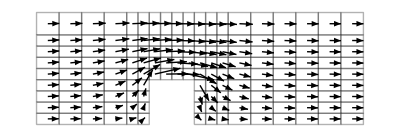

streamlines.eps

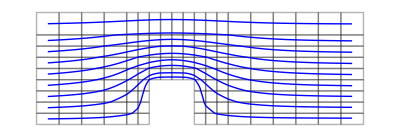

```mathematica
(*Solve the linear system*)
a=LinearSolve[Kij,Ri];
(*Postprocessing*)
(*Flow field*)
vectorArray = ConstantArray[0,{Length[elementRecord]}];

(*Given an element, plot the vector from the centroid of the element given by ∇ϕ*)
For[elt=1,elt≤Length[elementRecord],elt++,
α=getLocation[getNodes[elt][[1]]][[1]];
β=getLocation[getNodes[elt][[1]]][[2]];
γ=getLocation[getNodes[elt][[3]]][[1]];
δ=getLocation[getNodes[elt][[3]]][[2]];
cx=(α+γ)/2;
cy=(β+δ)/2;

(*Polynomial interpolation of the vector potential*)
ϕ[x_,y_]:=Sum[a[[getNodes[elt][[i]]]]*Ne[i,α,β,γ,δ,x,y],{i, 1, 4}];
flow=D[ϕ[x,y],{{x,y}}]/.{x-> cx,y-> cy};
vectorArray[[elt]] = Arrow[{{cx, cy},{cx,cy}+flow*scale}];
]
(*Streamline*)
plotPoints=ConstantArray[{},height];

(*For each element on the left edge, draw a streamline across*)
For[lineIndex=1,lineIndex ≤height,lineIndex++,

lastElement=Length[elementRecord]+1-lineIndex;
α=getLocation[getNodes[lastElement][[1]]][[1]];
γ=getLocation[getNodes[lastElement][[3]]][[1]];
endx=(α+γ)/2;

currentElement=lineIndex;
α=getLocation[getNodes[lineIndex][[1]]][[1]];
β=getLocation[getNodes[lineIndex][[1]]][[2]];
γ=getLocation[getNodes[lineIndex][[3]]][[1]];
δ=getLocation[getNodes[lineIndex][[3]]][[2]];

ξ=(α+γ)/2;
η=(β+δ)/2;

(*Iterate from left to right*)
While[ξ<endx,
elt=1;
plotPoints[[lineIndex]]=Append[plotPoints[[lineIndex]],{ξ,η}];
ϕ[x_,y_]:=Sum[a[[getNodes[currentElement][[i]]]]*Ne[i,α,β,γ,δ,x,y],{i, 1, 4}];
{Δξ,Δη}={Δx,Δy}*D[ϕ[x,y],{{x,y}}]/.{x-> ξ,y->η};
{ξ,η}={ξ,η}+{Δξ,Δη};

(*Continuing the streamline through element boundaries*)
If[ξ>γ,
(*Find the element to the right of this one*)
While[getNodes[elt][[1]]≠getNodes[currentElement][[2]],
If[elt>Length[elementRecord],Break[]];
elt++;
];
currentElement=elt;
];
If[η>δ,
(*Find the element above this one*)
While[getNodes[elt][[1]]≠getNodes[currentElement][[4]],
If[elt>Length[elementRecord],Break[]];
elt++;
];
currentElement=elt;
];
If[η<β,
(*Find the element below this one*)
While[getNodes[elt][[4]]≠getNodes[currentElement][[1]],
If[elt>Length[elementRecord],Break[]];
elt++;
];
currentElement=elt;
];

α=getLocation[getNodes[currentElement][[1]]][[1]];
β=getLocation[getNodes[currentElement][[1]]][[2]];
γ=getLocation[getNodes[currentElement][[3]]][[1]];
δ=getLocation[getNodes[currentElement][[3]]][[2]];
]
]
(*Flow field plot*)
flowField = {Graphics[{Arrowheads[Small],vectorArray}],Graphics[{Opacity[.3],lineArray}]};
Export["flowfield.eps", flowField];
Show[flowField,ImageSize-> Full]
(*Streamlines*)
streamLines = {Graphics[{Opacity[.3],lineArray}],ListCurvePathPlot[plotPoints, PlotStyle -> Blue]};
Export["streamlines.eps",streamLines]
Show[streamLines,ImageSize-> Full]
```